```mathematica
k={{1},{0}, {0}};
k1={{0},{1}, {0}};
k2={{0},{0}, {1}};
kkk=List[k,k1,k2];
k//MatrixForm
kk=List[k,k1];
For[i=0,i<3,i++,kk[[i]]=kkk[[i+1]];Print[kk[[i]]]]
```

(1
0
0)

{{1},{0},{0}}

{{0},{1},{0}}

{{0},{0},{1}}

```mathematica
For[i=0,i<3,i++,For[j=i+1,j<3,j++, R=Part[kk,i].Part[kk,j]†+Part[kk,j].Part[kk,i]†;Print[i,j,"  ",R//MatrixForm]]]
```

01  (0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

02  (0 | 0 | 1
0 | 0 | 0
1 | 0 | 0)

12  (0 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

```mathematica
CC=Range[9]; 
CC[[1]]=KroneckerProduct[Part[kk,0] , Part[kk,0]] . KroneckerProduct[Part[kk,0]† ,Part[kk,(0)]†];
CC[[2]]=KroneckerProduct[Part[kk,0] , Part[kk,1]] . KroneckerProduct[Part[kk,0]† ,Part[kk,(1)]†];
CC[[3]]=KroneckerProduct[Part[kk,0] , Part[kk,2]] . KroneckerProduct[Part[kk,0]† ,Part[kk,(2)]†];
For[i=1,i<3,i++,For[j=0,j<3,j++,R=KroneckerProduct[Part[kk,i] , Part[kk,j]] . KroneckerProduct[Part[kk,i]† ,Part[kk,(j-i)]†];CC[[(3*i)+j+1]]=R;]]
```

```mathematica
CNOT=0;
For[i=1,i≤9,i++,CNOT=CNOT+CC[[i]]];
CNOT//MatrixForm
Inverse[CNOT.CNOT]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
ω=Exp[2 π ⅈ/3];
H3=1/(√3){{1,1,1},{1,ω,ω^2},{1,ω^2,ω^4}};
X3={{0,0,1},{1,0,0},{0,1,0}};
Z3={{1,0,0},{0,ω,0},{0,0,ω^2}};
I3=IdentityMatrix[3];
CZ={{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0}};
XX=KroneckerProduct[X3.k,k,X3.k]//MatrixForm
CZ//MatrixForm
```

(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
X=Range[10];
X[[1]]=KroneckerProduct[I3.k2,I3.k,I3.k]
X[[2]]=KroneckerProduct[I3,H3,I3].X[[1]]
X[[3]]=KroneckerProduct[I3,CNOT].X[[2]]
X[[4]]=KroneckerProduct[CNOT,I3].X[[3]]
X[[5]]=KroneckerProduct[CNOT,I3].X[[4]]
X[[6]]=KroneckerProduct[H3,I3,I3].X[[5]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√3)},{0},{0},{1/(√3)},{0},{0},{1/(√3)},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√3)},{0},{0},{0},{1/(√3)},{0},{0},{0},{1/(√3)}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√3)},{0},{0},{0},{1/(√3)},{1/(√3)},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√3)},{1/(√3)},{0},{0},{0},{1/(√3)},{0}}

{{0},{0},{1/3},{1/3},{0},{0},{0},{1/3},{0},{0},{0},{1/3 ⅇ^(-(2 ⅈ π)/3)},{1/3 ⅇ^(-(2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^(-(2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^((2 ⅈ π)/3)},{1/3 ⅇ^((2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^((2 ⅈ π)/3)},{0}}

{{0},{0},{1/3},{1/3},{0},{0},{0},{1/3},{0},{0},{0},{1/3 ⅇ^(-(2 ⅈ π)/3)},{1/3 ⅇ^(-(2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^(-(2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^((2 ⅈ π)/3)},{1/3 ⅇ^((2 ⅈ π)/3)},{0},{0},{0},{1/3 ⅇ^((2 ⅈ π)/3)},{0}}

{{0},{0},{1/3},{1/3},{0},{0},{0},{1/3},{0},{0},{0},{1/3},{1/3},{0},{0},{0},{1/3},{0},{0},{0},{1/3},{1/3},{0},{0},{0},{1/3},{0}}

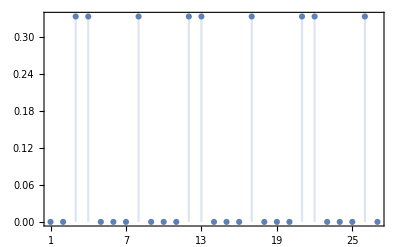

```mathematica
datapts=X[[6]]
For[i=1,i≤27,i++,If[datapts[[i,1]]≠0,datapts[[i,1]]=1/3,datapts[[i,1]]=0]]
datapts
DiscretePlot[datapts[[i,1]],{i,1,27},Frame->True,FrameTicks->{{Automatic,Automatic},{Range[1,27,1],Automatic}}]
```